## Chapter 1 : Introduction to Mathematica

## 1.1 Why Mathematica

## 1.2 The Wolfram Language

## 1.3 Structure of Mathematica

### 1.3.1 Design of Mathematica

```mathematica
(11*17)+(4/2)
```

189

## 1.4 Mathematica Environment

### 1.4.1 Notebook Interface

### 1.4.2 Text Processing

### 1.4.3 Palettes

### 1.4.4 Notebook Style and Features

```mathematica
Table[i^12,{i,1,10^4}]
```

## 1.5 Expression in Mathematica

### Expression in Mathematica

```mathematica
(3*3)+(4/2)
```

11

```mathematica
100^2*10
```

100000

```mathematica
2 1
```

2

```mathematica
1/2+√2
```

1/2+√2

```mathematica
N[1/2+√2]
```

1.91421

```mathematica
N[77/13,10]
```

5.923076923

```mathematica
4./2+2/13
```

2.15385

```mathematica
11/7;Sqrt[4]
```

2

```mathematica
3*4;100*100;Sqrt[4];Power[2,2];
```

### 1.5.1 Assigning Values

```mathematica
a=Pi
x=11
z+y
```

π

11

y+z

```mathematica
%12
In[12]
Out[12]
```

π

π

π

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
Module[{l=1,k=2,h=3},h √(k+l)+k+l]
```

3+3 √3

```mathematica
{l,k,h}
```

{l,k,h}

```mathematica
Clear[a,x]
```

```mathematica
Head[a]
```

Symbol

### 1.5.2 Built-in Functions

```mathematica
RandomInteger[]
```

1

```mathematica
Sin[90 Degree]+Cos[0 Degree]
```

2

```mathematica
Power[2,2]
```

4

```mathematica
d=Power[2,2]
 F=Sin[π]+Cos[π]
```

4

-1

```mathematica
Clear[d,F]
```

```mathematica
Options[RandomReal]
```

{WorkingPrecision→MachinePrecision}

```mathematica
RandomReal[{0,1},WorkingPrecision->MachinePrecision]
RandomReal[{0,1},WorkingPrecision->30]
```

0.0755815

0.22922264583310505159008771943

```mathematica
Options[Power]
```

{}

### 1.5.3 Dates and Time

```mathematica
DateObject[]
```

Tue 14 Nov 2023 18:04:06GMT-6

```mathematica
Tomorrow
```

Wed 15 Nov 2023

```mathematica
DateString[DateObject[{2020,6,10}]]
```

Wed 10 Jun 2020

```mathematica
DateString[DateObject[Today,CalendarType->"Julian"]]
DateString[DateObject[Today,CalendarType->"Jewish"]]
```

Tue 1 Nov 2023

Yom Shlishi 1 Kislev 5784

```mathematica
DateString[DateObject[{2010,3,4},TimeZone->"America/Belize"]]
```

Thu 4 Mar 2010

```mathematica
DateString[Sunset[Here,Now]]
DateString[Sunrise[Here,Yesterday]]
```

Wed 15 Nov 2023 17:58:17

Mon 13 Nov 2023 06:43:20

```mathematica
TimeObject[]
```

18:07:09TimeObject[{18,7,9.05257},Instant]

```mathematica
DateString[TimeZoneConvert[TimeObject[{17,0,0},TimeZone->"America/Cancun"],"America/Los_Angeles"]]
```

14:00:00

### 1.5.4 Strings

```mathematica
"Hello World" (*This is a comment*)
```

Hello World

```mathematica
ToString[23.423563]
```

23.4236

```mathematica
%//Head(*We use Head to know what type of object is*)
```

String

```mathematica
"Welcome to Mathematica"
```

Welcome to Mathematica

```mathematica
AtomQ["The sky is blue and tomorrow is expected to rain"]
```

True

```mathematica
Characters["Hello World"] (*Function that breaks the string into its characters*)
```

{H,e,l,l,o, ,W,o,r,l,d}

```mathematica
StringReplace["Hello this is a string ",{"h","H"}->"4"] (*This function repalce the string each time it appears for rule of the pattern,that is 4*)
```

4ello t4is is a string

```mathematica
ToUpperCase["hello my name is"]
```

HELLO MY NAME IS

```mathematica
ToLowerCase["HELLO MY NAME IS"]
```

hello my name is

```mathematica
StringJoin["Nice","to","have","you","back"]
```

Nicetohaveyouback

```mathematica
"Nice"<>"to"<>"have"<>"you"<>"back"
```

Nicetohaveyouback

### 1.5.5 Basic Plotting

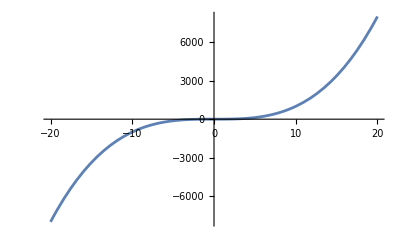

```mathematica
Plot[x^3,{x,-20,20}]
```

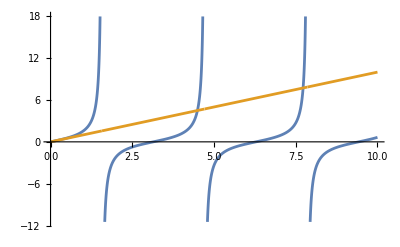

```mathematica
Plot[{Tan[x],x},{x,0,10}]
```

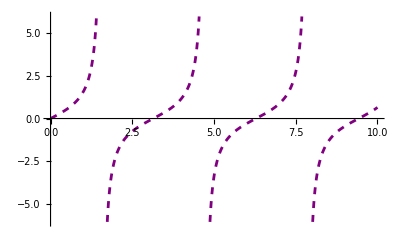

```mathematica
Plot[Tan[x],{x,0,10},PlotStyle->{Dashed,Purple}]
```

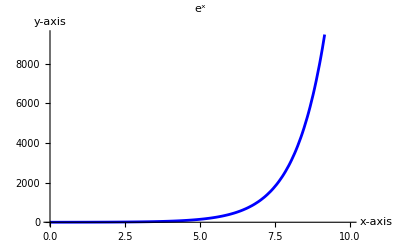

```mathematica
Plot[E^x,{x,0,10},PlotStyle->{Blue},PlotLabel->"e^x",AxesLabel->{"x-axis","y-axis"}]
```

### 1.5.6 Logical Operators and Infix Notation

```mathematica
6*1>2
```

True

```mathematica
6*1<2
```

False

```mathematica
1/2>=1/2
```

True

```mathematica
1/4<=1/2
```

True

```mathematica
3.12==2.72
```

False

```mathematica
π!=√-1
```

True

```mathematica
2===2.
```

False

```mathematica
2==1&&3.12==2
```

False

```mathematica
2*2==3||23*2==1
```

False

```mathematica
2==1⊻2==2
```

True

```mathematica
Power[1,2]⧦1^2
```

True

```mathematica
¬2==1
```

True

```mathematica
IntegerQ[1]
IntegerQ[1.]
```

True

False

```mathematica
AtomQ[12]
```

True

### 1.5.7 Algebraic Expressions

```mathematica
Expand[((x^2)+y^2)*(x+y)]
```

x^3+x^2 y+x y^2+y^3

```mathematica
Expand[a x^2*(a x)^3]
```

a^4 x^5

```mathematica
Simplify[x^3+x^2 y+x y^2+y^3]
FullSimplify[x^3+x^2 y+x y^2+y^3]
```

x^3+x^2 y+x y^2+y^3

(x+y) (x^2+y^2)

```mathematica
Together[1/z+1/(z+1)-1/(z+2)]
Apart[(2+4 z+z^2)/(z (1+z) (2+z))]
```

(2+4 z+z^2)/(z (1+z) (2+z))

1/z+1/(1+z)-1/(2+z)

### 1.5.8 Solving Algebraic Equations

```mathematica
Solve[z^2+1==2,z]
```

{{z→-1},{z→1}}

```mathematica
z^2+1/.Rule[z,{1,-1}]
```

{2,2}

```mathematica
{1^2+1==2,(-1)^2+1==2}
```

{True,True}

```mathematica
Solve[{x+y+z==2,6x-4y+5z==3,x+2y+2z==1},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

```mathematica
EQ1=x+y+z==2;EQ2=6 x-4 y+5 z==3;EQ3=x+2 y+2 z==1;
Solve[{EQ1,EQ2,EQ3},{x,y,z}]
```

{{x→3,y→10/9,z→-19/9}}

```mathematica
Solve[{x+y+z==a,6x-4y+5z==b,x+2y+2z==c},{x,y,z}]
```

{{x→2 a-c,y→1/9 (7 a-b-c),z→1/9 (-16 a+b+10 c)}}

```mathematica
Solve[EQ1&&EQ2,{x,y}]
```

{{x→1/10 (11-9 z),y→(9-z)/10}}

```mathematica
Solve[x^2+y^2==0||x-2y==1,x]
```

{{x→-ⅈ y},{x→ⅈ y},{x→1+2 y}}

```mathematica
Solve[z^-2+1==2&&z!=1,z]
```

{{z→-1}}

```mathematica
Reduce[Cos[x]==-1,x]
```

C[1]∈ℤ&&(x==-π+2 π C[1]||x==π+2 π C[1])

```mathematica
Reduce[h^2+k^2<11,{h,k}]
```

-√11<h<√11&&-√(11-h^2)<k<√(11-h^2)

```mathematica
Reduce[α+β * α^2==E,α]
```

(β==0&&α==ⅇ)||(β≠0&&(α==(-1-√(1+4 ⅇ β))/(2 β)||α==(-1+√(1+4 ⅇ β))/(2 β)))

### 1.5.9 Using Wolfram Alpha Inside Mathematica

Solve x^2+y^2== 1 && y+2x==0 ,for {x,y}

WolframAlphaQueryResults

WolframAlphaQueryParseResults

(x==-1/(√5)||x==1/(√5))&&y==-2 x

WolframAlphaQueryParseResults

TimeSeries[…]

WolframAlphaQueryParseResults

26400000 people

### 1.5.10 Delayed and Immediate Expressions

```mathematica
W=RandomReal[]
```

0.0886933

```mathematica
W==W
```

True

```mathematica
Clear[W];W:=RandomReal[];W
```

0.606234

```mathematica
W==W
```

False

```mathematica
z=2;               (*Assigning 2 to z*)
R=z->z^3;        (*Rule example*)
RD=z:>z^3;       (*RuleDelayed example*)
R
RD
```

2→8

2:>z^3

## 1.6 Improving Code

### 1.6.1 Code Performance

```mathematica
Timing[Power[10,10^8];]
```

{1.13884,Null}

```mathematica
Timing[10^10^8;]
```

{1.11997,Null}

```mathematica
AbsoluteTiming[10^10^8;]
```

{1.12004,Null}

```mathematica
AbsoluteTiming[Power[10,10^8];]
```

{1.12024,Null}

```mathematica
TimeConstrained[10^10^8,1]
```

$Aborted

```mathematica
EchoTiming[Power[10,10^8];,"Time in seconds:",Method->Timing]
EchoTiming[Power[10,10^8];,"Time in seconds:",Method->AbsoluteTiming]
```

"Time in seconds:"  1.12023

"Time in seconds:"  1.12074

### 1.6.2 Handling Errors

```mathematica
StringJoin["hello","I am ",Jeff]
```

StringJoin::string: String expected at position 2 in helloI am <>Jeff.

helloI am <>Jeff

```mathematica
Power[x/0,2]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

### 1.6.3 Debugging Techniques

```mathematica
x=2;
Echo[x];x=x^2+1;
Echo[x];x=x^2+1;
Echo[x];
```

2

5

26

```mathematica
x=2;
Echo[x,"Initial Value: "];
x=x^2+1;
EchoLabel["First Iteration: "][x];
x=x^2+1;
EchoEvaluation[x=x^2+1,"Second Iteration: "->"Output :"];
```

Initial Value:   2

First Iteration:   5

"Second Iteration: "  x=x^2+1

"Output :"  677

```mathematica
x=2;
EchoTiming[Echo[x,"Initial Value: "]];
x=x^2+1;
EchoTiming[EchoLabel["First Iteration: "][x]];
x=x^2+1;
EchoTiming[EchoEvaluation[x=x^2+1,"Second Iteration: "->"Output :"]];
Clear[x];
```

Initial Value:   2

0.02973

First Iteration:   5

0.027704

"Second Iteration: "  x=x^2+1

"Output :"  677

0.036824

## 1.7 How Mathematica Works

### 1.7.1 How Computations are Made (Form of Input)

```mathematica
StandardForm[1/x+x^2]
```

1/x+x^2

```mathematica
{InputForm[1/x+x^2],InputForm[a^x],InputForm[Subscript[a, x]],InputForm [√2]}
```

{x^(-1) + x^2,a^x,Subscript[a, x],Sqrt[2]}

```mathematica
FullForm[t/2+2^2]
```

Plus[4,Times[Rational[1,2],t]]

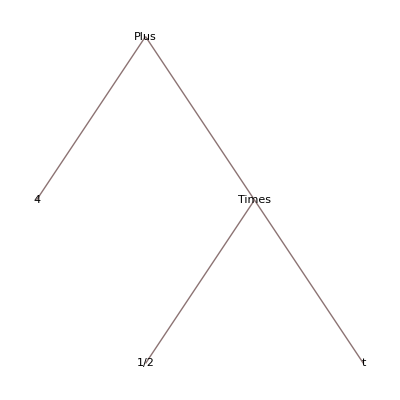

```mathematica
t/2+2^2//TreeForm
```

```mathematica
Trace[Plus[4,Times[Rational[1,2],t]]]
```

{{{Rational[1,2],1/2},t/2},4+t/2}

```mathematica
FullForm[Trace[Plus[4,Times[Rational[1,2],t]]]]
```

List[List[List[HoldForm[Rational[1,2]],HoldForm[Rational[1,2]]],HoldForm[Times[Rational[1,2],t]]],HoldForm[Plus[4,Times[Rational[1,2],t]]]]

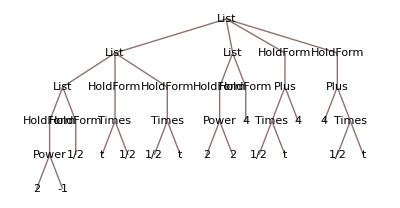

```mathematica
Trace[t/2+2^2]//TreeForm
```

### 1.7.2 Searching for Assistance

```mathematica
?Head
```

```mathematica
?Hea*
```

### 1.7.3 Notebook Security

```mathematica
$BaseDirectory
```

/Library/Mathematica

```mathematica
$UserBaseDirectory
```

/Users/macosx/Library/Mathematica

```mathematica
$InitialDirectory
```

/Users/macosx